```mathematica
Counting of sparsity :
```

Here we discuss how the sparsity varies with the dimension of the matrix.

### Two qubit

We start with a two qubit system where the initial density matrix is,

```mathematica
Clear[RHO,a,b,PauliUnitary]
Clear[a1,a2,θ]
RHO[a1_,a2_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}}]
L = Length[ArrayRules[SparseArray[RHO[a,b]]]/.Rule->List]-1;
Sparsity = L/(2^2)^2;
Hint = {{0,0,0,0},{0,0,I,0},{0,-I, 0,0},{0,0,0,0}};
U=MatrixExp[- I Hint θ]//FullSimplify
PauliUnitary[k_]:= KroneckerProduct[IdentityMatrix[1],UPauli[k],IdentityMatrix[1]] 
UPauli[k_]:= MatrixExp[- I PauliMatrix[k]]//FullSimplify
$Assumptions ={θ,ϕ,a1,a2} ∈Reals
RHOT = PauliUnitary[1].RHO[a1,a2].Transpose[PauliUnitary[1]]//FullSimplify;
KroneckerProduct[Identity[1],PauliMatrix[1]]
```

{{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}}

(θ|ϕ|a1|a2)∈ℝ

Dot::dotsh: Tensors {{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}} and {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} have incompatible shapes.

Dot::dotsh: Tensors {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} and {{Cos[1],-ⅈ Sin[1]},{-ⅈ Sin[1],Cos[1]}} have incompatible shapes.

KroneckerProduct::rect: Nonrectangular array encountered.

KroneckerProduct[1,{{0,1},{1,0}}]

```mathematica
cde3\
```

```mathematica
SparseArray[RHOT];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^2)^2 ;
Print[16]
Print[ L]
Print[Lt]
Print[N[Sparsity]]
Print[N[SparsityT]]
TraceSystem[RHOT,2]//FullSimplify
Pop[a1_,a2_,θ_
]:= 1/2 (a1+a2+(a1-a2) Cos[2 θ]);
WorkExtractable= Temp[Pop[at,a2,θ]]((1-Pop[a1,adummy,θ])Log[(1-Pop[a1,adummy,θ])/(1-Pop[at,a2,θ])]  + (Pop[a1,adummy,θ])Log[(Pop[a1,adummy,θ])/(Pop[at,a2,θ])]  )-Temp[at]((1-a1)Log[(1-a1)/(1-at)]  + (a1)Log[(a1)/(at)]  );
For[Work= WorkExtractable;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];at=RandomReal[{0.0001,0.4999}];adummy=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= WorkExtractable; If[Work>0,Print[Work],Null];Clear[Work,a1,a2,at,θ]]
```

Clear::ssym: RHO.Work is not a symbol or a string.

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{1-a,0},{0,a}},{{{1,-2},0},{0,{0,3}}}]].

ArrayRules::rect: Nonrectangular array encountered.

{{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}}

(θ|ϕ|a1|a2)∈ℝ

Dot::dotsh: Tensors {{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}} and {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} have incompatible shapes.

Dot::dotsh: Tensors {{(1-a1) (1-a2),0,0,0},{0,(1-a1) a2,0,0},{0,0,a1 (1-a2),0},{0,0,0,a1 a2}} and {{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}} have incompatible shapes.

SparseArray::list: List expected at position 1 in SparseArray[{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}.{{(-1+a1) (-1+a2),0,0,0},{0,a2-a1 a2,0,0},{0,0,a1-a1 a2,0},{0,0,0,a1 a2}}.{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}].

ArrayRules::rect: Nonrectangular array encountered.

16

0

0

0.

0.

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}.{{(-1+a1) (-1+a2),0,0,0},{0,a2-a1 a2,0,0},{0,0,a1-a1 a2,0},{0,0,0,a1 a2}}.{{Cos[θ],-ⅈ Sin[θ]},{-ⅈ Sin[θ],Cos[θ]}}

0.0347876

0.0659128

0.0554759

0.830837

0.0244158

0.15012

0.0327844

0.0145658

0.0452402

0.0510971

0.00252075

0.0192539

0.093971

0.0663017

0.024619

0.00206227

0.00465454

1.40642

0.127786

0.0168943

0.0102077

0.00985564

0.103802

0.0011367

0.00153111

0.019865

0.000173941

0.00840514

15.8665

0.0782707

0.379289

0.0116671

0.103816

0.125494

0.0343512

0.00188956

0.0239509

0.00972607

0.000546617

0.00791905

0.00789595

0.028405

0.0117876

0.0126458

2.76784

0.0783934

0.0994474

0.797692

0.0625088

0.00798953

0.0547849

0.0869533

0.00520976

0.00199781

0.0196081

0.136882

0.0000880251

0.190859

0.00467069

0.0166055

0.0367022

0.0316849

1.79986

0.0179171

0.0203161

0.00342179

0.000189336

0.00188309

0.000642034

0.0413144

0.00119741

0.0147763

0.00412346

3.46595×10^-6

0.00428221

0.00708821

0.0562059

0.0110632

0.150503

0.0246685

0.000836826

0.00769103

0.000954018

7.14935×10^-7

0.0349948

0.00686341

0.235647

0.0318026

0.0275395

0.00434079

0.107103

0.00036747

3.56897×10^-8

0.0268644

0.0316643

0.00309286

0.0508617

0.0532153

12.5521

0.00371184

0.00240123

0.209727

0.0013048

0.0511589

0.000284721

0.00146307

0.00401222

0.00359028

0.115497

0.0213212

0.0642331

0.00795047

0.791878

```mathematica
cd\00de3
```

```mathematica
cd\0e30
```

```mathematica
Tinitial = TraceSystem[RHO[a1,a2],{1}];
Tfinal = TraceSystem[RHOTmachtrial,{1}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify
```

```mathematica
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
```

```mathematica
RHOsysInitial= TraceSystem[RHO[a1,a2],{2}]//FullSimplify;
RHOmachInitial= TraceSystem[RHO[a2,a2],{2}]//FullSimplify;
```

```mathematica
RHOsysFinal= TraceSystem[RHOTsystrial,{2}]//FullSimplify;
```

```mathematica
A1 =Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial = Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]- Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
```

```mathematica
Clear[a1,a2,t,Wex]
```

```mathematica
Wex = WFinal-WInitial;
```

ArcTanh[1-2 a2] (a1+a2+(a1-a2) Cos[2 t])+(-1+a1) Log[1-a1]-a1 Log[a1]-Log[1-a2]-(-1+a1) Log[1-a2]+a1 Log[a2]+1/2 ((a1+a2+(a1-a2) Cos[2 t]) Log[1/2 (a1+a2+(a1-a2) Cos[2 t])]-(-2+a1+a2+(a1-a2) Cos[2 t]) Log[1/2 (2-a1-a2+(-a1+a2) Cos[2 t])])

```mathematica
Clear[a1,a2,t,Work]
For[Work= Wex;i=1, i<15,i++,Work=Wex;a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,t]]
```

### Three qubit

We now look at the sparsity of three qubits

```mathematica
n=3;
Clear[RHO,a1,a2,a3,RHOT]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
```

```mathematica
RHOlabel = {{A1,0,0,0,0,0,0,0},{0,A2,0,0,0,0,0,0},{0,0,A3,0,0,0,0,0},{0,0,0,A4,0,0,0,0},{0,0,0,0,A5,0,0,0},{0,0,0,0,0,A6,0,0},{0,0,0,0,0,0,A7,0},{0,0,0,0,0,0,0,A8}};
L = Length[ArrayRules[SparseArray[RHO[a,b,c]]]/.Rule->List]-1;
Sparsity = L/(2^n)^2;
Hint = -{{0,0,0,0,0,0,0,0},{0,0,I ,0,I ,0,0,0},{0,- I  ,0,0,I ,0,0,0},{0,0,0,0,0,I ,I ,0},{0,-I ,-I ,0,0,0,0,0},{0,0,0,-I ,0,0,I ,0},{0,0,0,-I ,0,-I ,0,0},{0,0,0,0,0,0,0,0}};
```

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{1-a,0},{0,a}},{{{1,-2},0},{0,{0,3}}},{{{0,-1,-2,-3},0},{0,{1,2,3,4}}}]].

ArrayRules::rect: Nonrectangular array encountered.

```mathematica
HintEnergysubsp1[G1_,G2_,G3_] := -{{0,0,0,0,0,0,0,0},{0,0,I G1,0,I G2,0,0,0},{0,- I G1 ,0,0,I G3,0,0,0},{0,0,0,0,0,0,0,0},{0,-I G2,-I G3,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
HintEnergysubsp2 [F1_,F2_,F3_] := -{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0 ,0,0,0,0,0,0},{0,0,0,0,0,I F1,I F2,0},{0,0,0,0,0,0,0,0},{0,0,0,-I F1,0,0,I F3,0},{0,0,0,-I F2,0,-I F3,0,0},{0,0,0,0,0,0,0,0}};
```

```mathematica
U1=MatrixExp[- I HintEnergysubsp1[1,0,0] θ]//FullSimplify;
U2=MatrixExp[- I HintEnergysubsp1[0,1,0] θ]//FullSimplify;
U3=MatrixExp[- I HintEnergysubsp1[0,0,1] θ]//FullSimplify;
U4=MatrixExp[- I HintEnergysubsp1[1,1,0] θ]//FullSimplify;
U5=MatrixExp[- I HintEnergysubsp1[1,0,1] θ]//FullSimplify;
U6=MatrixExp[- I HintEnergysubsp1[0,1,1] θ]//FullSimplify;
U7=MatrixExp[- I HintEnergysubsp1[1,1,1] θ]//FullSimplify;
U8=MatrixExp[- I HintEnergysubsp2[1,0,0] θ]//FullSimplify;
U9=MatrixExp[- I HintEnergysubsp2[0,1,0] θ]//FullSimplify;
U10=MatrixExp[- I HintEnergysubsp2[0,0,1] θ]//FullSimplify;
U11=MatrixExp[- I HintEnergysubsp2[1,1,0] θ]//FullSimplify;
U12=MatrixExp[- I HintEnergysubsp2[1,0,1] θ]//FullSimplify;
U13=MatrixExp[- I HintEnergysubsp2[0,1,1] θ]//FullSimplify;
U14=MatrixExp[- I HintEnergysubsp2[1,1,1] θ]//FullSimplify;
```

```mathematica
U=MatrixExp[- I Hint θ]//FullSimplify;
RHOT = U.RHO[a1,a2,a3].Transpose[U]//FullSimplify;
RHOTT = U.RHOT.Transpose[U];
```

```mathematica
SparseArray[RHOT];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^n)^2 ;
Print[64]
Print[ L]
Print[Lt]
Print[N[Sparsity]]
Print[N[SparsityT]]
MatrixForm[RHOTlabel]//FullSimplify;
MatrixForm[U]//FullSimplify;
```

64

0

20

0.

0.3125

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
Utrial=MatrixExp[- I Hint  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a2,a2,a3].Transpose[Utrial]//FullSimplify;
```

```mathematica
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
```

```mathematica
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
```

```mathematica
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOmachInitial= TraceSystem[RHO[a2,a2,a3],{2,3}]//FullSimplify;
```

```mathematica
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; If[Work>0,Print[Work],Null];Clear[Work,a1,a2,a3,t]]
```

Unitary1

```mathematica
Temp[h_]:= Temp[h] = 1/(Log[(1-h)/h]);
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U1.RHO[a1,a2,a3].Transpose[U1]//FullSimplify;
RHOTmachtrial = U1.RHO[a2,a2,a3].Transpose[U1]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

```mathematica
LinguisticAssistant
```

Unitary2

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U2.RHO[a1,a2,a3].Transpose[U2]//FullSimplify;
RHOTmachtrial = U2.RHO[a2,a2,a3].Transpose[U2]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 3

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U3.RHO[a1,a2,a3].Transpose[U3]//FullSimplify;
RHOTmachtrial = U3.RHO[a2,a2,a3].Transpose[U3]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 4

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U4.RHO[a1,a2,a3].Transpose[U4]//FullSimplify;
RHOTmachtrial = U4.RHO[a2,a2,a3].Transpose[U4]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary5

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U5.RHO[a1,a2,a3].Transpose[U5]//FullSimplify;
RHOTmachtrial = U5.RHO[a2,a2,a3].Transpose[U5]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 6

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U6.RHO[a1,a2,a3].Transpose[U6]//FullSimplify;
RHOTmachtrial = U6.RHO[a2,a2,a3].Transpose[U6]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 7

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U7.RHO[a1,a2,a3].Transpose[U7]//FullSimplify;
RHOTmachtrial = U7.RHO[a2,a2,a3].Transpose[U7]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 8

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U8.RHO[a1,a2,a3].Transpose[U8]//FullSimplify;
RHOTmachtrial = U8.RHO[a2,a2,a3].Transpose[U8]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 9

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U9.RHO[a1,a2,a3].Transpose[U9]//FullSimplify;
RHOTmachtrial = U9.RHO[a2,a2,a3].Transpose[U9]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 10

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U10.RHO[a1,a2,a3].Transpose[U10]//FullSimplify;
RHOTmachtrial = U10.RHO[a2,a2,a3].Transpose[U10]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 11

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U11.RHO[a1,a2,a3].Transpose[U11]//FullSimplify;
RHOTmachtrial = U11.RHO[a2,a2,a3].Transpose[U11]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<50000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 12

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U12.RHO[a1,a2,a3].Transpose[U12]//FullSimplify;
RHOTmachtrial = U12.RHO[a2,a2,a3].Transpose[U12]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 13

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U13.RHO[a1,a2,a3].Transpose[U13]//FullSimplify;
RHOTmachtrial = U13.RHO[a2,a2,a3].Transpose[U13]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]
```

Unitary 14

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,θ,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}]
RHOTsystrial = U14.RHO[a1,a2,a3].Transpose[U14]//FullSimplify;
RHOTmachtrial = U14.RHO[a2,a2,a3].Transpose[U14]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3],{1,3}]//FullSimplify;
Tfinal = TraceSystem[RHOTmachtrial,{2,3}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3],{2,3}]//FullSimplify;
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3}]//FullSimplify;
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
For[Work= Wex;i=1, i<500,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];θ=RandomReal[{0,2π}];
Work= Wex; If[Work>10^-10,Print[Work],Null];Clear[Work,a1,a2,a3,θ]]3
```

We suspect that the rise in the non zero elements comes from the pair-wise correlations one must now consider. Recall that for the two qubit case, the hermiticity of the density matrices implied that to each correlation that would develop the number of non-zero elements in the matrix goes up by two. SImilarly now, considering all the interactions that can introduce correlations i.e. both in energy subspace 1 and energy subspace 2, we have 6 interactions which implies that the number of nonzero elements goes up by 12 and indeed that is the trend that the matrix follows. Based on this, we expect that in the four qubit case the number of non zero elements would go up by 54 elements (non zero elements initially = 16, total elements = 54+16=70 which gives sparsity to be 0.273438).

### Four qubit

We now look at the sparsity of four qubits

```mathematica
n=4;
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
```

```mathematica
L = Length[ArrayRules[SparseArray[RHO[a,b,c,d]]]/.Rule->List]-1;
Sparsity = L/(2^n)^2;
HintEnergysubsp14Q = SparseArray[{{2,3}->I,{3,2}->-I,{2,5}->I,{5,2}->-I,{2,9}->I,{9,2}->-I,{3,5}->I,{5,3}->-I,{3,9}->I,{9,3}->-I,{5,9}->I,{9,5}->-I},{16,16}];
HintEnergysubsp24Q = SparseArray[{{4,6}->I,{4,7}->I,{4,10}->I,{4,11}->I,{4,13}->I,{6,4}->-I,{7,4}->-I,{10,4}->-I,{11,4}->-I,{13,4}->-I,{6,7}->I,{6,10}->I,{6,11}->I,{6,13}->I,{7,6}->-I,{10,6}->-I,{11,6}->-I,{13,6}->-I,{7,10}->I,{7,11}->I,{7,13}->I,{10,7}->-I,{11,7}->-I,{13,7}->-I,{10,11}->I,{10,13}->I,{11,10}->-I,{13,10}->-I,{11,13}->I,{13,11}->-I},{16,16}];
HintEnergysubsp34Q = SparseArray[{{8,12}->I,{8,14}->I,{8,15}->I,{12,8}->-I,{14,8}->-I,{15,8}->-I,{12,14}->I,{12,15}->I,{14,15}->I,{14,12}->-I,{15,14}->-I,{15,12}->-I},{16,16}];
U1=MatrixExp[- I HintEnergysubsp14Q  θ]//FullSimplify;
U2=MatrixExp[- I HintEnergysubsp24Q  θ]//FullSimplify;
U3=MatrixExp[- I HintEnergysubsp34Q  θ]//FullSimplify;
```

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{1-a,0},{0,a}},{{{1,-2},0},{0,{0,3}}},{{{0,-1,-2,-3},0},{0,{1,2,3,4}}},{{1-d,0},{0,d}}]].

ArrayRules::rect: Nonrectangular array encountered.

4

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
HintTrial = SparseArray[{{4,13}->I,{13,4}->-I},{16,16}];
Utrial=MatrixExp[- I HintTrial  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3,a4].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a3,a3,a1,a2].Transpose[Utrial]//FullSimplify;
```

```mathematica
0c\0\0\000cd\00cd\0cd\00\0\0e3c\0cd\0cde30cde3\cd\00cde3\cde3\0c\0cd\0\00cde3
```

```mathematica
Clear[a1,a4,a2,a3]
Tinitial = TraceSystem[RHO[a1,a2,a3,a4],{1,2,4}];
Tfinal = TraceSystem[RHOTmachtrial,{2,3,4}]//FullSimplify
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
```

Under such a mechanism things are actually gibbs preserving. So the temperature maybe takes from eithe the fisrt or the second machine qubits.

```mathematica
RHOthInitial = KroneckerProduct[{{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}},{{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}}];
RHOsysInitial= TraceSystem[RHO[a1,a2,a3,a4],{3,4}];
```

```mathematica
RHOthFinal = KroneckerProduct[{{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}},{{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}}];
RHOsysFinal= TraceSystem[RHOTsystrial,{3,4}];
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
```

```mathematica
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
```

```mathematica
Clear[W4qb,Popa1]
For[Work= Wex;i=1, i<1000,i++,a1=RandomReal[{0.0001,0.4999}];a2=RandomReal[{0.0001,0.4999}];a3=RandomReal[{0.0001,0.4999}];a4=RandomReal[{0.0001,0.4999}];t=RandomReal[{0,2π}];
Work= Wex; If[Work>0 ,{Popa1[i_]:=Popa1[i]=Abs[a1-a3]+Abs[a3-a2]+Abs[a3-a4];Table[Popa1[i],i];W4qb[i_] :=W4qb[i]= Work;Table[W4qb[i],i]},Null];Clear[Work,a1,a2,a3,a4,t]];
ListPlot[Table[{i,W4qb[i]},{i,1000}]]
ListPlot[Table[{Popa1[i],i},{i,1000}]]
```

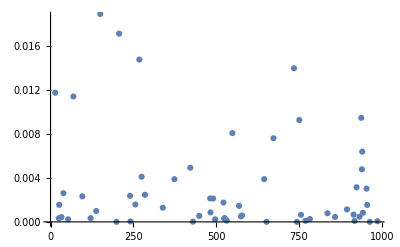
```mathematica
-Graphics-c\03
```

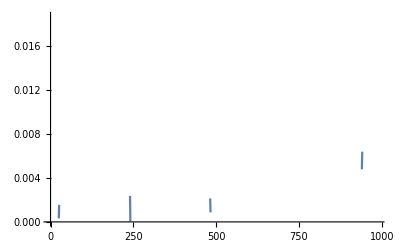

```mathematica
ListLinePlot[Table[{i,W4qb[i]},{i,1000}]]
```

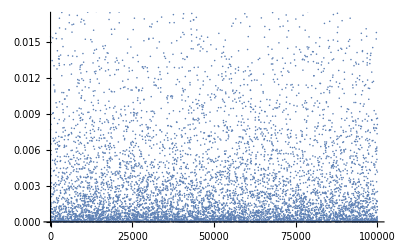

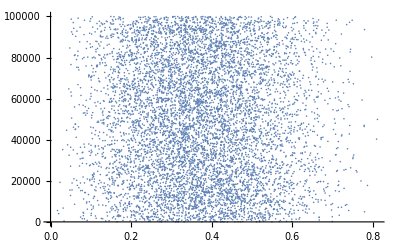

```mathematica
Clear[RHO,a1,a2,a3,t,A1,A2,WInitial,WFinal,Wex,RHOTmachtrial,RHOTsystrial,Utrial,Tinitial,Tfinal,TempInitial,TempFinal]
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
HintTrial = SparseArray[{{4,13}->I,{13,4}->-I},{16,16}];
Utrial=MatrixExp[- I HintTrial  t]//FullSimplify;
RHOTsystrial = Utrial.RHO[a1,a2,a3,a4].Transpose[Utrial]//FullSimplify;
RHOTmachtrial = Utrial.RHO[a2,a2,a3,a4].Transpose[Utrial]//FullSimplify;
Tinitial = TraceSystem[RHO[a1,a2,a3,a4],{1,3,4}];
Tfinal = TraceSystem[RHOTmachtrial,{2,3,4}]//FullSimplify;
TempInitial= Temp[Tinitial[[2,2]]]//FullSimplify;
TempFinal= Temp[Tfinal[[2,2]]]//FullSimplify;
RHOthInitial = {{1-Tinitial[[2,2]],0},{0,Tinitial[[2,2]]}};
RHOsysInitial= TraceSystem[RHO[a1,a2,a3,a4],{2,3,4}];
RHOthFinal = {{1-Tfinal[[2,2]],0},{0,Tfinal[[2,2]]}};
RHOsysFinal= TraceSystem[RHOTsystrial,{2,3,4}];
```

```mathematica
A1 =TempFinal* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = TempFinal* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
WInitial =  TempInitial*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  TempInitial* Tr[RHOsysInitial.MatrixLog[RHOthInitial]]//FullSimplify;
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<15,i++,a1=RandomReal[{0,0.5}];a2=RandomReal[{0,0.5}];a3=RandomReal[{0,0.5}];a4=RandomReal[{0,0.5}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,a3,a4,t]]
```

-0.0471793

-0.00259779

-0.0140545

-0.00045888

-0.00614344

-6.05687×10^-6

-0.0112478

-0.0266996

-3.3347×10^-7

-0.0419091

-0.0260043

-0.000205066

-0.0118421

-0.989501

```mathematica
A1 =Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]//FullSimplify;
A2 = Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOthFinal]]//FullSimplify;
```

```mathematica
WFinal=A1-A2;
```

```mathematica
Wex = WFinal-WInitial;
```

```mathematica
For[Work= Wex;i=1, i<15,i++,a1=RandomReal[{0,0.5}];a2=RandomReal[{0,0.5}];a3=RandomReal[{0,0.5}];a4=RandomReal[{0,0.5}];t=RandomReal[{0,2π}];
Work= Wex; Print[Work];Clear[Work,a1,a2,a3,a4,t]]
```

0.0896663

0.0101749

0.0446598

-0.0366336

-0.176829

0.0349666

-0.0276198

0.0462237

-0.044243

0.0346091

0.0418401

0.0349405

0.032455

0.0221544

```mathematica
Manipulate[Plot[WFinal,{t,0,8}],{a1,0.0001,0.4999},{a4,0.0001,0.4999}]
```

```mathematica
WInitial =  Tinitial[[2,2]]*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  Tinitial[[2,2]]* Tr[RHOthInitial.MatrixLog[RHOthInitial]]//FullSimplify
```

-a3 ((-1+a1+a2-a1 a2) Log[(-1+a1) (-1+a2)]-a1 a2 Log[a1 a2]+a1 (-1+a2) Log[a1-a1 a2]+(-1+a1) a2 Log[a2-a1 a2]+(-1+a3) ((-1+a3) Log[(-1+a3)^2]-2 a3 Log[-(-1+a3) a3])+a3^2 Log[a3^2])

```mathematica
Simplify[WFinal]
```

```mathematica
Wex =FullSimplify[ Tfinal[[2,2]]* Tr[RHOsysFinal.MatrixLog[RHOsysFinal]]- Tfinal[[2,2]]* Tr[RHOthFinal.MatrixLog[RHOthFinal]]-( Tinitial[[2,2]]*Tr[RHOsysInitial.MatrixLog[RHOsysInitial]]-  Tinitial[[2,2]]* Tr[RHOthInitial.MatrixLog[RHOthInitial]])]
```

```mathematica
Manipulate[Plot[Wex,{ θ,0,8}],{a1,0,0.5},{a4,0,0.5}]
```

```mathematica
RHOT1 = U1.RHO[a1,a2,a3,a4].Transpose[U1]//FullSimplify;
RHOT2 = U2.RHO[a1,a2,a3,a4].Transpose[U2]//FullSimplify;
RHOT3 = U3.RHO[a1,a2,a3,a4].Transpose[U3]//FullSimplify;
RHOT = RHOT1 +RHOT2+RHOT3
SparseArray[RHOT1];
Lt = Length[ArrayRules[SparseArray[RHOT]]/.Rule->List]-1;
SparsityT = Lt/(2^n)^2 ;cde3
Print[64];
Print[ L];
Print[Lt];
Print[N[Sparsity]];
Print[N[SparsityT]];
```

64

8

0

0.125

0.

For general n-qubit system, we can define a protocol for the allowed interactions in the energy subspaces starting with energy subspace E=1, 2,...n-1. For any energy subspace the energy comes from a qubit being in the 1 state. Therefore, the number of terms per energy subspace can be generated by allowing as many 1’s while all other qubits being in 0. This is a simple nCq combinatorics problem where q = energy subspace. For eg. number of pure states in energy subspace 1 is nC1. Then the number of terms in interaction would be pairwise combination of these temrs without repeating which is simple \sigma (nC1 -1) +(cN1 -2)+(nC1 -3)...+(1). Then the number of correlation produced by these interactions would be double the number of interactions available. So sparsity would be a function of this n as, 
{\Sigma_{E=1}^{n-1} (nCE-1)(nCE) + 2^n}{(2^2n}

# 16-qubit system

SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])

This is my attempt at performing 16 qubit rotations.  We will first begin with defining an uncorrelated initial density matrix for the 16 qubits as:

```mathematica
RHO[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_,a13_,a14_,a15_,a16_] := KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}},{{1-a5,0},{0,a5}},{{1-a6,0},{0,a6}},{{1-a7,0},{0,a7}},{{1-a8,0},{0,a8}},{{1-a9,0},{0,a9}},{{1-a10,0},{0,a10}},{{1-a11,0},{0,a11}},{{1-a12,0},{0,a12}},{{1-a13,0},{0,a13}},{{1-a14,0},{0,a14}},{{1-a15,0},{0,a15}},{{1-a16,0},{0,a16}}]
U
```

```mathematica
U123=KroneckerProduct[U,IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[2]];
U234=KroneckerProduct[IdentityMatrix[2],U,IdentityMatrix[2],IdentityMatrix[2]];
U345=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],U,IdentityMatrix[2]];
U456=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],IdentityMatrix[2],U];
```

```mathematica
RHO[a1_,a2_,a3_,a4_,a5_,a6_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}},{{1-a5,0},{0,a5}},{{1-a6,0},{0,a6}}];
For[i=1  ; RHOT =RHO,
i<15,
i++;Unitary=RandomChoice[{U123,U234,U345,U456}];ConjUnitary=Transpose[Unitary];RHOT=Unitary.RHOT.ConjUnitary;
RHOT1=TraceSystem[RHOT,{2,3,4,5,6}];
RHOT2=TraceSystem[RHOT,{1,3,4,5,6}];
RHOT3=TraceSystem[RHOT,{1,2,4,5,6}];
RHOT4=TraceSystem[RHOT,{1,2,3,5,6}];
RHOT5=TraceSystem[RHOT,{1,2,3,4,6}];
RHOT6=TraceSystem[RHOT,{1,2,3,4,5}],
Print[RHOT1];Print[RHOT2];Print[RHOT3];Print[RHOT4];Print[RHOT5];Print[RHOT6]]
```

```mathematica
RHO[a1_,a2_,a3_,a4_]:=KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
RHO[a1,a2,a3,a4]
```

```mathematica
SparseArray[%66]
```

```mathematica
For[i=1  ; RHOT =RHO,
i<5,
i++;Unitary=RandomChoice[{U123,U234}];ConjUnitary=Transpose[Unitary];RHOT=Unitary.RHOT.ConjUnitary;
RHOT1=TraceSystem[RHOT,{2,3,4}];
RHOT2=TraceSystem[RHOT,{1,3,4}];
RHOT3=TraceSystem[RHOT,{1,2,4}];
RHOT4=TraceSystem[RHOT,{1,2,3}],
Print[RHOT1];Print[RHOT2];Print[RHOT3];Print[RHOT4]]
```

```mathematica
DensityMatrix[q_] := {{1-q,0},{0,q}}
```

```mathematica
Clear[q1,q2,a,b,R]
RelEntBetweenQubits[q1_,q2_,q1t_,q2t_] :=Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q1]]] - Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q2]]]-(Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q1t]]] - Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q2t]]])
RelEntBetweenQubits[0.1,0.3,q1t,q2t]
FreeEn [q1_,q2_,q1t_,q2t_] :=-Temp[q2](Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q1]]] - Tr[DensityMatrix[q1].MatrixLog[DensityMatrix[q2]]])+Temp[q2t](Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q1t]]] - Tr[DensityMatrix[q1t].MatrixLog[DensityMatrix[q2t]]])
```

```mathematica
DistanceBetweenQubits[q1_,q2_,q1t_,q2t_,E_]:=-(Abs[q1t-q2t]+Abs[2q1t-E+q2t]+Abs[2q2t-E+q1t])+Abs[q1-q2]+Abs[2q1-E+q2]+Abs[2q2-E+q1]
DistanceBetweenQubits[0.1,0.3,0.12,0.32,0.8]
FreeEn[0.1,0.3,0.12,0.32]
RelEntBetweenQubits[0.1,0.3,0.12,0.32]
```

0.12

0.00757275

0.00713165

```mathematica
FindInstance[Dis,{q1t,q2t}]
```

$Aborted

```mathematica
Temp[h_]:= 1/(Log[(1-h)/h])
```

```mathematica
RegionPlot3D[ {R-(0.11632-(1-q1t) Log[1-q1t]-q1t Log[q1t]+(1-q1t) Log[1-q2t]+q1t Log[q2t])≥ 0,R-(0.8-Abs[q1t-q2t]-Abs[-0.8+2 q1t+q2t]-Abs[-0.8-q1t+2 q2t])≥0},{q1t,0,0.5},{q2t,0,0.5},{R,0,100}]
```

RegionPlot3D::boolf: {R-(0.11632-Plus[«2»] Log[«1»]-q1t Log[«1»]+(1+Times[«2»]) Log[Plus[«2»]]+q1t Log[q2t])≥0,R-(0.8-Abs[Plus[«2»]]-Abs[Plus[«3»]]-Abs[Plus[«3»]])≥0} must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D[{R-(0.11632-(1-q1t) Log[1-q1t]-q1t Log[q1t]+(1-q1t) Log[1-q2t]+q1t Log[q2t])≥0,R-(0.8-Abs[q1t-q2t]-Abs[-0.8+2 q1t+q2t]-Abs[-0.8-q1t+2 q2t])≥0},{q1t,0,0.5},{q2t,0,0.5},{R,0,100}]

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

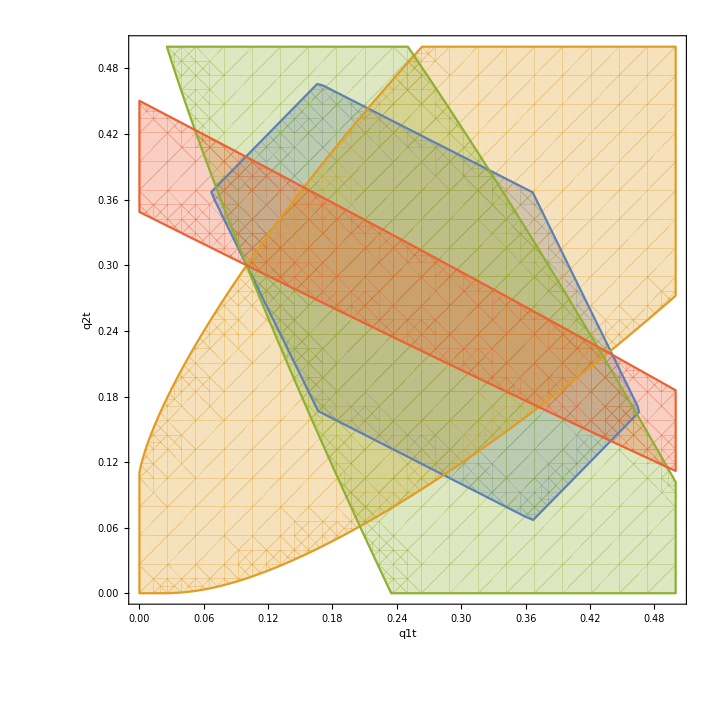

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

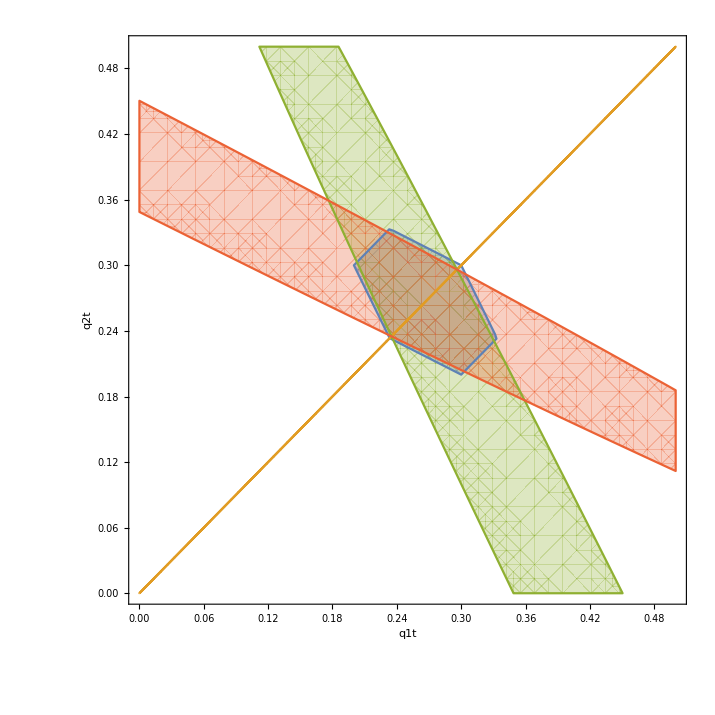

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.000785399+1.57048 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 0.205474+1.57048 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

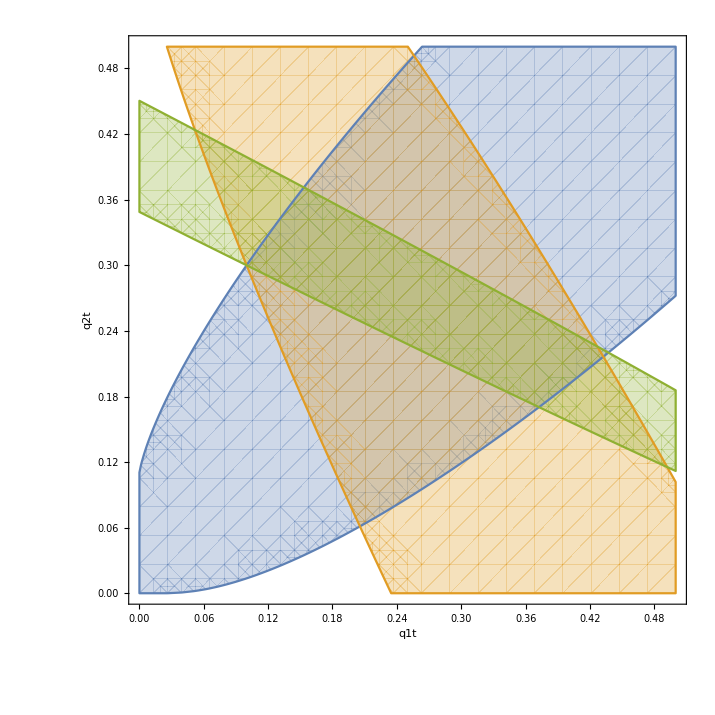

```mathematica
Plot3D[{DistanceBetweenQubits[0.1,0.3,q1t,q2t,0.8],RelEntBetweenQubits[0.1,0.3,q1t,q2t], FreeEn[0.1,0.3,q1t,q2t]},{q1t,0,0.5},{q2t,0,0.5},PlotRange->{0,10}];

RegionPlot[{DistanceBetweenQubits[0.1,0.3,q1t,q2t,0.8]≥ 0,RelEntBetweenQubits[0.1,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.1,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]
RegionPlot[{DistanceBetweenQubits[0.3,0.3,q1t,q2t,0.8]≥ 0,RelEntBetweenQubits[0.3,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.3,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]

RegionPlot[{RelEntBetweenQubits[0.1,0.3,q1t,q2t]≥0,RelEntBetweenQubits[0.1,0.4,q1t,0.8-(q1t+q2t)]≥0,RelEntBetweenQubits[0.3,0.4,q2t,0.8-(q1t+q2t)]≥0},{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, AxesLabel->Automatic]
```

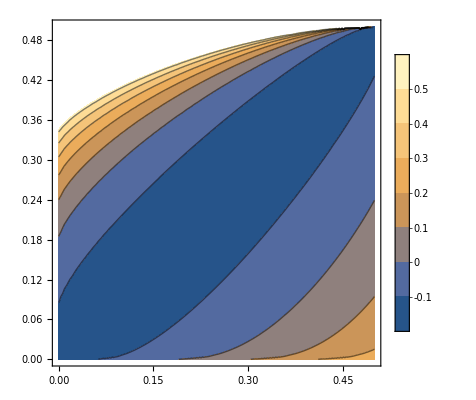

```mathematica
ContourPlot[FreeEn[0.1,0.3,q1t,q2t],{q1t,0.0001,0.4999},{q2t,0.0001,0.4999}, PlotLegends->Automatic]
```

```mathematica
RHOT//FullSimplify;
TargetQubit = TraceSystem[RHOT,{2,3}];
```

```mathematica
PopFinal[a1_,a2_,a3_,θ_] := 1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))
```

```mathematica
Q2t = PopFinal[a2,a2,a3,θ]//FullSimplify
Q1t = PopFinal[a1,a2,a3,θ]//FullSimplify
```

1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))

1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))

```mathematica
W = WexFinal-WexInitial;

θ=π/4
RegionPlot3D[W≥0,{a1,0.0001,0.4999},{a2,0.0001,0.4999},{a3,0.0001,0.4999}]
ContourPlot3D[{WexFinal,WexInitial},{a1,0.0001,0.4999},{a2,0.0001,0.4999},{a3,0.0001,0.4999}]
```

π/4

-Graphics3D-

```mathematica
WexFinal = Temp[Q2t](Tr[DensityMatrix[Q1t](MatrixLog[DensityMatrix[Q1t]]-MatrixLog[DensityMatrix[Q2t]])])
```

((-Log[1/9 (9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (1+1/9 (-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))+1/9 (-Log[1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))/Log[(9 (1+1/9 (-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))))/(3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+√3 (-1+2 a2) (2 Sin[√3 θ]-Sin[2 √3 θ])))]

```mathematica
Simplify[WexFinal]
```

((-Log[1/9 (9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (9-3 (a1+a2+a3)-(4 a1-2 (a2+a3)) Cos[√3 θ]-(2 a1-a2-a3) Cos[2 √3 θ]-√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))+(-Log[1/9 (3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))]+Log[1/9 (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ]))]) (3 (a1+a2+a3)+(4 a1-2 (a2+a3)) Cos[√3 θ]+(2 a1-a2-a3) Cos[2 √3 θ]+√3 (-1+2 a1) (a2-a3) (2 Sin[√3 θ]-Sin[2 √3 θ])))/(9 Log[(9-3 (2 a2+a3)-(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))/(3 (2 a2+a3)+(a2-a3) (2 Cos[√3 θ]+Cos[2 √3 θ]+4 √3 (-1+2 a2) Sin[(√3 θ)/2]^2 Sin[√3 θ]))])

```mathematica
WexInitial = Temp[a2](Tr[DensityMatrix[a1](MatrixLog[DensityMatrix[a1]]-MatrixLog[DensityMatrix[a2]])]) //FullSimplify
```

(-(-1+a1) (Log[1-a1]-Log[1-a2])+a1 (Log[a1]-Log[a2]))/Log[-1+1/a2]